# Streamline Processor

```mathematica
workingDirectory=NotebookDirectory[];
If[!DirectoryQ[workingDirectory],CreateDirectory[workingDirectory]];
SetDirectory[workingDirectory];
```

```mathematica
matrixToString[matrix_]:=StringTrim/@StringJoin/@Table[ToString[matrix[[i,j]]]<>" ",{i,Length[matrix]},{j,Length[matrix[[i]]]}]
```

```mathematica
listInputFile = SystemDialogInput["FileOpen",workingDirectory];
edgeList = If[Length[listInputFile]==0,{listInputFile},listInputFile];
```

```mathematica
edges=ToExpression/@Import[listInputFile,"List"]
Length[edges]
```

47022

133068

```mathematica
Length[DeleteDuplicates[edges]]
```

47022

```mathematica
coordinateAssociation=<||>;
nodeCounter=0;
Table[If[KeyExistsQ[coordinateAssociation,edges[[i,1]]],,AssociateTo[coordinateAssociation,edges[[i,1]]->++nodeCounter]];If[KeyExistsQ[coordinateAssociation,edges[[i,2]]],,AssociateTo[coordinateAssociation,edges[[i,2]]->++nodeCounter]];Nothing,{i,Length[edges]}];
nodeAssociation=Association@KeyValueMap[#2->#1&,coordinateAssociation];
```

SparseArray[…]

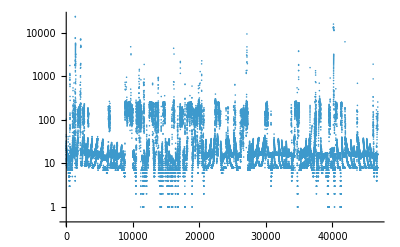

-Graphics-

{24,26}

False

```mathematica
directedEdges=True;
adjustEdges=False;
makeEdgeWeightsInteger=False;
weightedEdges=If[directedEdges==False,SparseArray[Join@@Table[With[{start=coordinateAssociation[edges[[i,1]]],end=coordinateAssociation[edges[[i,2]]]},{{start,end}->edges[[i,3]],{end,start}->edges[[i,3]]}],{i,Length[edges]}]],SparseArray[Join@@Table[With[{start=coordinateAssociation[edges[[i,1]]],end=coordinateAssociation[edges[[i,2]]]},{{start,end}->edges[[i,3]]}],{i,Length[edges]}]]]
ListLogPlot[weightedEdges["ExplicitValues"]]
If[adjustEdges,weightedEdges=weightedEdges*1/0.1];
If[makeEdgeWeightsInteger,weightedEdges=Ceiling[weightedEdges]];
ListLogPlot[weightedEdges["ExplicitValues"]]
(*For checking symmetry of the matrix, both should have values non-zero*)
With[{a=1,b=2},{weightedEdges[[b,a]],
weightedEdges[[a,b]]}]
SymmetricMatrixQ[weightedEdges]
```

```mathematica
weightsPDF=PDF[EmpiricalDistribution[weightedEdges["ExplicitValues"]],x];
```

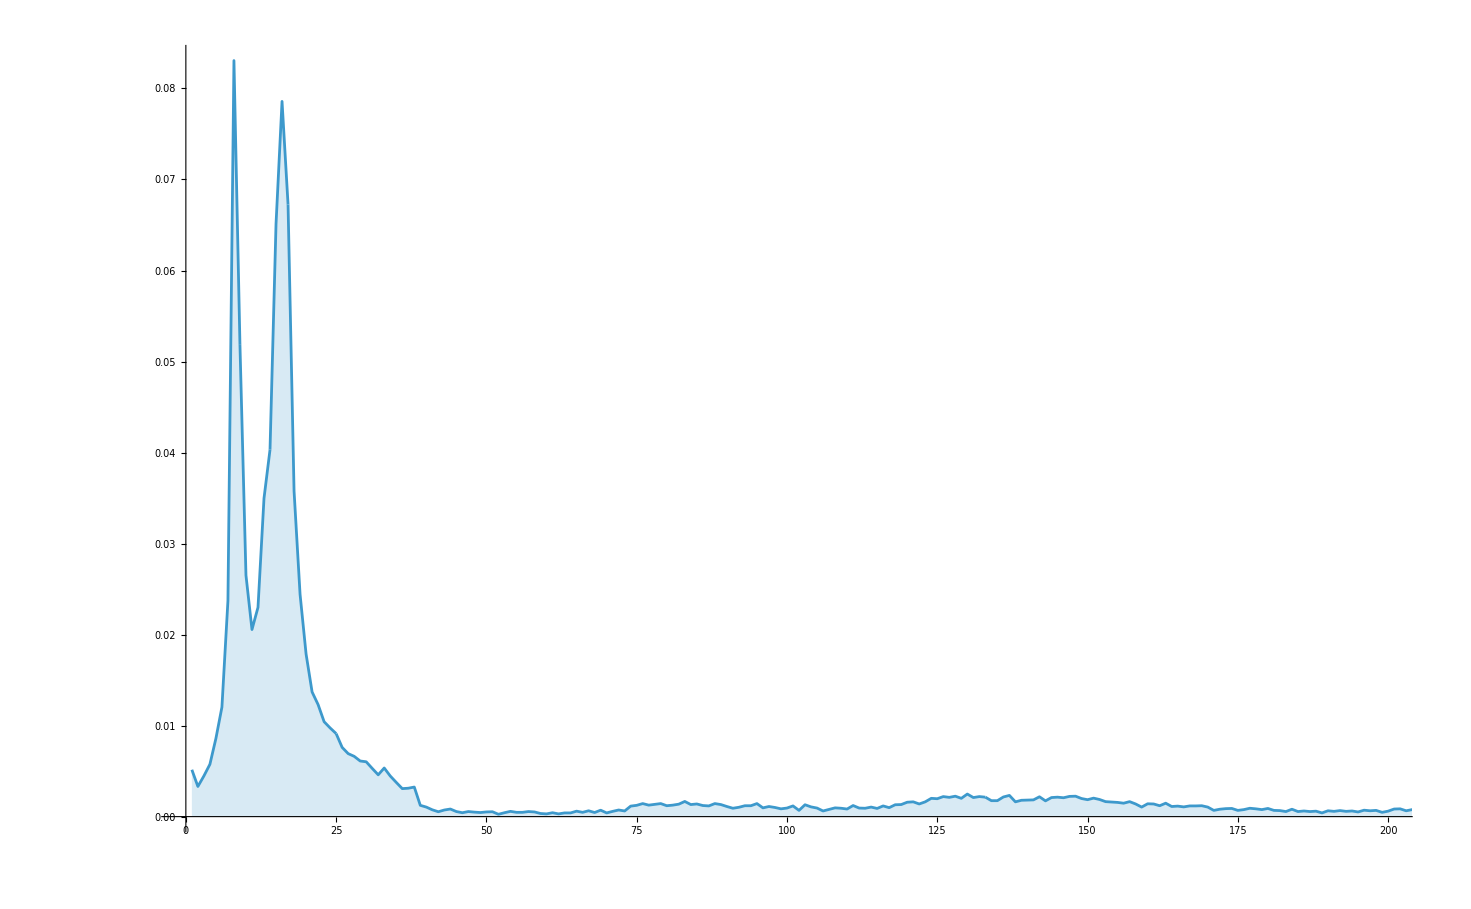

```mathematica
DiscretePlot[weightsPDF,{x,weightedEdges["ExplicitValues"]},PlotRange->{{0,200},All}]
```

```mathematica
graph=Graph[WeightedAdjacencyGraph[SparseArray[Join[ArrayRules[weightedEdges][[1;;-2]],{{_,_}->Infinity}]]],VertexCoordinates->Normal[nodeAssociation]];
```

```mathematica
graph
```

```mathematica
CompleteGraphQ[graph]
```

False

```mathematica
FindHamiltonianCycle[graph]
```

```mathematica
mathematicaHamDefault =
```

```mathematica
Max[VertexDegree[graph]]
Length[EdgeList[graph]]
VertexList[graph]//Short
Length[VertexList[graph]]
AnnotationValue[graph,EdgeWeight]//Short
Max[AnnotationValue[graph,EdgeWeight]]
Length[AnnotationValue[graph,EdgeWeight]]
AnnotationValue[graph, VertexCoordinates]//Short
Length[AnnotationValue[graph, VertexCoordinates]]
Thread[EdgeList[graph]->AnnotationValue[graph,EdgeWeight]]/.DirectedEdge[u_,v_]:>{u,v}
```

82

46821

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,«7848»,7866,7867,7868,7869,7870,7871,7872,7873,7874,7875,7876,7877,7878,7879,7880,7881,7882}

7882

{26,25,27,45,103,24,22,41,16,16,15,25,29,13,12,29,20,12,23,20,«46781»,135,16,16,8,8,139,16,17,8,59,61,110,98,63,76,71,139,196,256,154}

23486

46821

{{23.,75.4279},{23.15,75.35},«7878»,{103.889,36.3459},{105.895,35.6024}}

7882

## New method to convert to json file for NX

```mathematica
graphToJson[graph_]:=
	Module[
		{numPts=Length[VertexList[graph]], maxDegree=Max[VertexDegree[graph]],
		 numEdges=Length[EdgeList[graph]], coords=AnnotationValue[graph, VertexCoordinates],
		 vertexList=VertexList[graph], edgeList=AnnotationValue[graph,EdgeWeight],
		 edgeWeights=Thread[EdgeList[graph]->AnnotationValue[graph,EdgeWeight]],
		 maxEWeight=Max[AnnotationValue[graph,EdgeWeight]]
		},
		<|{"n"->numPts, "d"->maxDegree, "m"->numEdges,
		   "E"->edgeList, "V"->vertexList, "Vcoords"->coords,
		   "Eweights"->edgeWeights, "MaxEWeight"->maxEWeight
		}|>
	]
```

```mathematica
jsonCleanup[jsonAssociation_]:=
	Module[
		{adjustedAssociation = jsonAssociation, cleanEdgeWeights},
		(*Make a clean version of the edge weights where key is String,String*)
		cleanEdgeWeights = KeyMap[ToString[#[[1]]]<>","<>ToString[#[[2]]]&,Association[adjustedAssociation["Eweights"]]];
		AppendTo[adjustedAssociation,"Eweights"->cleanEdgeWeights];
		(*Replace directed/undirected edges with arrays*)
		adjustedAssociation = adjustedAssociation/.DirectedEdge[u_,v_]:>{u,v};
		adjustedAssociation = adjustedAssociation/.UndirectedEdge[u_,v_]:>{u,v};
		(*Return as a list of associations for now*)
		{adjustedAssociation}
	]
```

```mathematica
Export[workingDirectory <>FileBaseName[listInputFile]<>ToString["_graph.json"],jsonCleanup[graphToJson[graph]],"JSON"]
```

R:\data\tsp_nx\graph_making\2025-12-10_GA-List14_graph.json

## Validation

```mathematica
ResourceData["GraphHighlightStyle"]
```

{Automatic,Dashed,Dotted,Thick,VertexConcaveDiamond,VertexDiamond,VertexTriangle,DehighlightFade,DehighlightGray,DehighlightHide}

```mathematica
greedyPathCSV=SystemDialogInput["FileOpen",workingDirectory];
```

```mathematica
greedyPath=Import[greedyPathCSV,"List"];
```

```mathematica
HighlightGraph[graph,PathGraph[greedyPath,DirectedEdges->True],GraphHighlightStyle->"DehighlightHide"]
```

-Graphics-

```mathematica
chrisPathCSV=SystemDialogInput["FileOpen",workingDirectory];
```

```mathematica
chrisPath=Import[chrisPathCSV,"List"];
```

```mathematica
HighlightGraph[graph,PathGraph[chrisPath,DirectedEdges->True],GraphHighlightStyle->"DehighlightHide"]
```

-Graphics-

## Old method to convert to a string file

```mathematica
stringMatrix=matrixToString[weightedEdges];
```

```mathematica
outputName="ga-list11";
Export[NotebookDirectory[]<>outputName<>"_AM.txt",stringMatrix,"List"]
Export[NotebookDirectory[]<>outputName<>"_nodeList.wl",nodeAssociation]
Export[NotebookDirectory[]<>outputName<>"_coordList.wl",coordinateAssociation]
Export[NotebookDirectory[]<>outputName<>"_sparseEdgeArray.wl",weightedEdges]
```

C:\Users\Ian\OneDrive - The University of Texas at El Paso\Joint Lab\Independent\2025\11\Joseph November GA Runs\ga-list11_AM.txt

C:\Users\Ian\OneDrive - The University of Texas at El Paso\Joint Lab\Independent\2025\11\Joseph November GA Runs\ga-list11_nodeList.wl

C:\Users\Ian\OneDrive - The University of Texas at El Paso\Joint Lab\Independent\2025\11\Joseph November GA Runs\ga-list11_coordList.wl

C:\Users\Ian\OneDrive - The University of Texas at El Paso\Joint Lab\Independent\2025\11\Joseph November GA Runs\ga-list11_sparseEdgeArray.wl

## Testing

```mathematica
edgeWeights=Thread[EdgeList[graph]->AnnotationValue[graph,EdgeWeight]]/.DirectedEdge[u_,v_]:>{u,v}
```

```mathematica
Select[edgeWeights,#[[1,1]]==7882&]
Select[edgeWeights,#[[1,1]]==7880&]
```

{{7882,6758}→196,{7882,7851}→256,{7882,7880}→154}

{{7880,6758}→59,{7880,7045}→61,{7880,7850}→110,{7880,7851}→98,{7880,7882}→63}

```mathematica
jsonCleanup[graphToJson[graph]][[1,"Eweights","7882,7880"]]
jsonCleanup[graphToJson[graph]][[1,"Eweights","7880,7882"]]
```

154

63